# Specific Potential For Schrodinger Equation

## Animation

## Potential Distribution

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Set::span: First[{}];;First[{}] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

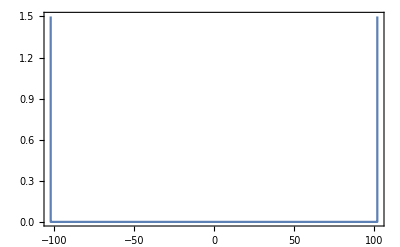

```mathematica
dt=0.01; Nsteps=50;T=120;hbar=1; m=1.9; ntotal=2^11; dx=0.1;
 x`vec=Table[-1/2*ntotal*dx+i*dx,{i,0,ntotal-1}]; 
{index1,index2}={First@Flatten@Position[x`vec,First@Select[x`vec,-width<#<width&]],First@Flatten@Position[x`vec,Last@Select[x`vec,-width<#<width&]]};

V0=1.5; L=hbar/(√(2m V0)); width=3L;  Vx=Table[0,{i,Length[x`vec]}]; Vx[[-1]]=Vx[[1]]=10^6;  Vx[[index1;;index2]]=V0;

potential=Table[{x`vec[[i]],Vx[[i]]},{i,1,ntotal}];
ListLinePlot[potential,PlotRange->{Automatic,{0,V0}},Frame->True]
```

```mathematica
x0=-60*L; E0=0.2*V0; p0=√(2m*E0); k0=p0/hbar; v0=p0/m; a=hbar/(√(2*(2m E0/80)));
gauss`x[x_,a_,x0_,k0_]:=1/(√(a √π))ⅇ^(-1/2((x-x0)/a)^2+ⅈ x k0);
```

```mathematica
f[x_,psi]:=ⅈ[(psi[x+dx,t]+psi[x-dx,t]-2psi[x,t])/(2dx^2)];
k1=f[x,psi];
k2=f[x,psi+dt/2 k1];
k3=f[x,psi+dt/2 k2];
k4=f[x,psi+dt k3];
```

```mathematica
T=10;dt=T/10^3;data={};
y=1;
f[t_,y_]:=t √y;
k1[t_]:=N@f[t,y]dt;
k2[t_]:=N@f[t+dt/2,y+k1[t]/2]dt;
k3[t_]:=N@f[t+dt/2,y+k2[t]/2]dt;
k4[t_]:=N@f[t+dt,y+k3[t]]dt;
Do[AppendTo[data,y];y=y+1/6(k1[t]+2k2[t]+2k3[t]+k4[t]),{t,0,T-dt,dt}];
```

```mathematica
ClearAll[y,k1,k2,k3,k4]
```

## Definition for wave functions

```mathematica
gauss`x[x_,a_,x0_,k0_]:=1/(√(a √π))ⅇ^(-1/2((x-x0)/a)^2+ⅈ k0 x);
gauss`k[k_,a_,x0_,k0_]:=1/(√(a √π))ⅇ^(-1/2(a(k-k0))^2-ⅈ x0 (k-k0));
```

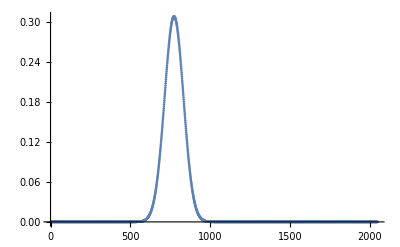

```mathematica
ListPlot[Map[Norm,gauss`x[x`vec,a,x0,k0]],PlotRange->All]
```

```mathematica
gauss`x[x`vec,a,x0,k0]
```

{-2.81735×10^-38-2.02182×10^-38 ⅈ,-3.2224×10^-38-2.87933×10^-38 ⅈ,-3.60937×10^-38-3.9945×10^-38 ⅈ,-3.93955×10^-38-5.42571×10^-38 ⅈ,-4.15729×10^-38-7.23983×10^-38 ⅈ,2039,-1.45459×10^-101+2.53314×10^-101 ⅈ,-1.19445×10^-101+1.64504×10^-101 ⅈ,-9.48287×10^-102+1.04947×10^-101 ⅈ,-7.33627×10^-102+6.55522×10^-102 ⅈ}
 |  |  |  |

```mathematica
dk=(2π)/(ntotal*dx); k`vec=Table[-1/2 ntotal*dk+i*dk,{i,0,ntotal-1}];
```

```mathematica
psi`x0[x_]:=gauss`x[x,a,x0,k0];
psi`x[x_]:=psi`0[x];
psi`discrete`x[x_]:=dx/(√(2π))psi`x[x]*ⅇ^(-ⅈ k`vec[[0]] x);
psi`x[x_]:=psi`discrete`x[x]*ⅇ^(ⅈ k`vec[[0]] x)*(√(2π))/dx;
```

## Different Potential’s EigenStates

### One Dimension

```mathematica
Schrodinger[{xmin_,xmax_},U_Function,NGrid_:101]:=Module[{dx=(xmax-xmin)/(NGrid-1),V`mat,T`mat,H`mat},
V`mat=DiagonalMatrix[U/@Range[xmin,xmax,dx]];
T`mat=DiagonalMatrix[Table[-1/(2(dx)^2)*(-2),NGrid]]+DiagonalMatrix[Table[-1/(2(dx)^2),NGrid-1],1]+DiagonalMatrix[Table[-1/(2(dx)^2),NGrid-1],-1];
H`mat=V`mat+T`mat;
Sort[Transpose[Eigensystem[N@H`mat]],#1[[1]]<#2[[1]]&]
];

Module[{},fun1=1/2#^2&;
fun2=Piecewise[{{100000,#<0},{1/2#^2,#>=0}}]&;
fun3=Piecewise[{{0,-7≤#<-5},{-20,-5≤#<-3},{0,-3<=#<-1},{-20,-1≤#≤1},{0,3>=#>1},{-20,3<#≤5},{0,5<#≤7}}]&;
fun4=1/2#^2+2Exp[-2#^2]&;]

Manipulate[pot`fun=Switch[d,1,fun1,2,fun2,3,fun3,4,fun4];
sol=Schrodinger[{-10,10},pot`fun,1000];
eigenvalues=Transpose[sol][[1]];
eigenvecs=sol[[1;;-1,2]];
f1=ListLinePlot[Table[2.5eigenvecs[[i]]+eigenvalues[[i]],{i,levels}],PlotRange->{{-10,10},All},DataRange->{-10,10},Axes->False,Frame->True,PlotStyle->Dashed];
f2=ListLinePlot[Table[{x,pot`fun[x]},{x,-10,10,20/1000}],PlotRange->All];
Grid[{{Grid[Table[{Subscript["E", i],eigenvalues[[i]]},{i,levels}],Frame->All],Show[f1,f2,ImageSize->Medium]}}],
{{d,1,"Potential Type"},{1,2,3,4}},
{{levels,5,"Number of Levels"},Range[1,10,1],ControlType->SetterBar}]
```

### Two Dimensions



```mathematica
Plot[Sin[x],{x,0,10}]
```